```mathematica
p=a x^2 + b x +c ==y
```

c+b x+a x^2==y

```mathematica
ans=FullSimplify[Solve[{p/.{y->0,x->xv+.5aa},p/.{y->0,x->xv-.5aa},p/.{y->ym,x->xv}},{a,b,c}]]
```

{{a→0.-(4. ym)/aa^2,b→(8. xv ym)/aa^2,c→(1.-(4. xv^2)/aa^2) ym}}

```mathematica
pi=ans/.{aa->3,xv->-3,ym->10}
```

{{a→-4.44444,b→-26.6667,c→-30.}}

```mathematica
p/.pi[[1]]
```

-30.-26.6667 x-4.44444 x^2==y

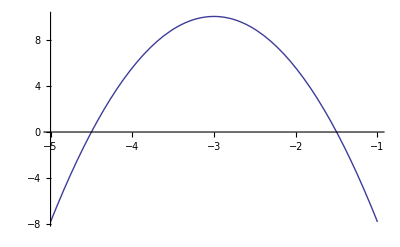

```mathematica
Plot[-30.-26.666666666666664 x-4.444444444444445 x^2,{x,-5,-1}]
```